## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[23]
```

{23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

## Topic

### Definition / Theorem

This is text.

#### Example

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,101,111}]//tf
```

101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

```mathematica
nQuotientToNatural[4/5]
nQuotientToNatural[3/5]
nQuotientToNatural[7/25]
nQuotientToNatural[24/25]
nQuotientToNatural[-44/125]
nQuotientToNatural[117/125]
nQuotientToNatural[-527/625]
nQuotientToNatural[336/625]
nQuotientToNatural[-3116/3125]
nQuotientToNatural[-237/3125]

(4/5+3/5I)^5
```

161

91

12251

144001

12100000

85556251

43395156250

17640000001

37927562500000

219410156250

-3116/3125-(237 ⅈ)/3125

```mathematica
nQuotientToNatural[5/11]
FactorInteger[551]
nIntegerToNatural[19]
```

551

{{19,1},{29,1}}

39

```mathematica
nQuotientToNatural[7/13]
FactorInteger[1275]
nIntegerToNatural[3]
nIntegerToNatural[25]
nIntegerToNatural[17]
```

1275

{{3,1},{5,2},{17,1}}

7

51

35

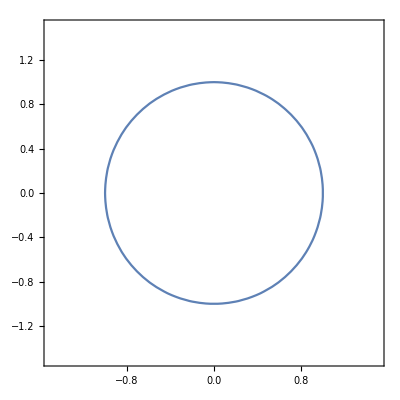

```mathematica
ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->Automatic]
```

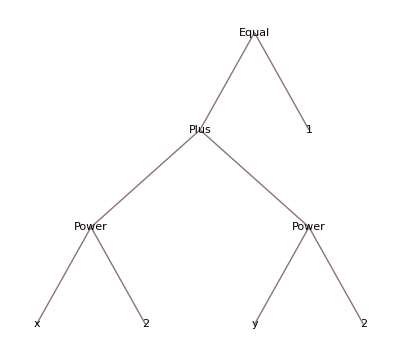

```mathematica
TreeForm[x^2+y^2==1]
```

## Ideas

## Reading Questions Ch.1

### Section 1.1

Q1 : When is a set S countable? When is it uncountable?

A1: A set S is countable when it has a finite cardinality, or when a bijection between ℕ and S can be established. S is uncountable otherwise.

Q2: Give an example of distinct finite sets X and Y with |X| = |Y|.

A2: X = { a,b,c } and Y = { 1,2,3 }.

Q3: Give an example of non-empty finite sets X and Y with |X| < |Y|.

A3: X = { a } and Y = { 1,2,3,4 }.

Q4: State The Countable Union Theorem and give an example of its use to prove an infinite set A is countable.

A4: The Countable Union Theorem: The union of a countable number of countable sets is countable.
[ TBD ]

Q5: What does the Continuum Hypothesis (CH) say? Is it True or False?

A5: The CH says: “There is no set whose cardinality is strictly between that of the natural numbers and the real numbers.”
In 1940 Kurt Gödel showed that the CH cannot be proved False.  In 1963 Paul Cohen showed that the CH cannot be proved True.

Q6: Give examples of three countably infinite sets.

A6: Three examples are ℕ, ℤ and ℚ.

Q7: Give examples of three uncountable sets.

A7: Three examples are ℝ, ℂ and [ TBD ].

### Section 1.2

Q1 : What is the definition of Lebesgue measure for an interval of real numbers with endpoints a and b?

A1: The Lebesgue measure of any interval is defined to be its length. m([a,b]) = b-a. 
This result also holds for open and half-open intervals.

Q2 : When does a set S have Lebesgue measure zero?

A2: A set S has Lebesgue measure zero when it can be covered with a sequence of open intervals I1, I2, I3,... whose bounded total measure is arbitrarily small. In this case, S is a null set and we write m(S) = 0. This basically means that given any ε > 0, S can be covered with a sequence of open intervals I1, I2, . . . , where ∑_(n=1)^∞ m(I_n)<=ϵ .

Q3 : Give an example of two Lebesgue measure-zero sets, at least one having an infinite number of elements.

A1: [ TBD ]

Q4 : Give an example of a Lebesgue measure zero uncountable set.

```mathematica
g[x_]:=x^2+2x+1
```

```mathematica
Mod[g[8],27]
Mod[g[8],9]
Mod[g[8],3]
```

0

0

0

```mathematica
Mod[g[17],27]
Mod[g[17],9]
Mod[g[17],3]
```

0

0

0

```mathematica
Mod[g[26],27]
Mod[g[26],9]
Mod[g[26],3]
```

0

0

0

```mathematica
Solve[x^2+2x+1==0,x,Modulus->9]
```

{{x→2},{x→5},{x→8}}

```mathematica
Solve[{x-2y==0,2x+y==4},{x,y},Modulus->7]
```

{{y→5,x→3}}

## Test-1

```mathematica
f[x_]:=x^3+5x +9
Table[{k,f[k],Mod[f[k],3]},{k,0,2}]//tf
Table[{k,f[k],Mod[f[k],5]},{k,0,4}]//tf
Solve[x^3+5x+9==0,x,Modulus->5]
Solve[x^3+5x+9==0,x,Modulus->9]
Solve[x^3+5x+9==0,x,Modulus->45]
```

0 | 9 | 0
1 | 15 | 0
2 | 27 | 0

0 | 9 | 4
1 | 15 | 0
2 | 27 | 2
3 | 51 | 1
4 | 93 | 3

{{x→1}}

{{x→0},{x→2},{x→7}}

{{x→11},{x→16},{x→36}}

## Test-2

```mathematica
StirlingS1[3,1]
```

2

```mathematica
PowerMod[13,-1,35]
```

27

```mathematica
Mod[4 91 73+2 65 28+11 35 27,455]
```

112

```mathematica
3 112
```

336

```mathematica
Solve[x^2+3x+17==0,x,Modulus->315]
```

{{x→29},{x→38},{x→94},{x→148},{x→164},{x→218},{x→274},{x→283}}

```mathematica
tls:={a,b,c,d}
```

```mathematica
Permutations[tls]//Length
```

24

## Test-3

```mathematica
Solve[x^2+x+1==0,x,Modulus->7]
Solve[x^2+x+1==0,x,Modulus->13]
ChineseRemainder[{2,9},{7,13}]
ChineseRemainder[{2,3},{7,13}]
ChineseRemainder[{4,9},{7,13}]
ChineseRemainder[{4,3},{7,13}]
Solve[x^2+x+1==0,x,Modulus->91]
```

{{x→2},{x→4}}

{{x→3},{x→9}}

9

16

74

81

{{x→9},{x→16},{x→74},{x→81}}

```mathematica
Solve[x^2+x+1==0,x,Modulus->(174307)]
Solve[x^2+x+1==0,x,Modulus->(175341)]
Solve[x^2+x+1==0,x,Modulus->(175981)]
```

{{x→417},{x→24483},{x→51403},{x→76304},{x→98002},{x→122903},{x→149823},{x→173889}}

{{x→3994},{x→15628},{x→159712},{x→171346}}

{{x→419},{x→67265},{x→108715},{x→175561}}

```mathematica
Table[{k,k^2+k+1,FactorInteger[k^2+k+1]},{k,1,423}]//tf
```

1 | 3 | 3 | 1
2 | 7 | 7 | 1
3 | 13 | 13 | 1
4 | 21 | 3 | 1
7 | 1
5 | 31 | 31 | 1
6 | 43 | 43 | 1
7 | 57 | 3 | 1
19 | 1
8 | 73 | 73 | 1
9 | 91 | 7 | 1
13 | 1
10 | 111 | 3 | 1
37 | 1
11 | 133 | 7 | 1
19 | 1
12 | 157 | 157 | 1
13 | 183 | 3 | 1
61 | 1
14 | 211 | 211 | 1
15 | 241 | 241 | 1
16 | 273 | 3 | 1
7 | 1
13 | 1
17 | 307 | 307 | 1
18 | 343 | 7 | 3
19 | 381 | 3 | 1
127 | 1
20 | 421 | 421 | 1
21 | 463 | 463 | 1
22 | 507 | 3 | 1
13 | 2
23 | 553 | 7 | 1
79 | 1
24 | 601 | 601 | 1
25 | 651 | 3 | 1
7 | 1
31 | 1
26 | 703 | 19 | 1
37 | 1
27 | 757 | 757 | 1
28 | 813 | 3 | 1
271 | 1
29 | 871 | 13 | 1
67 | 1
30 | 931 | 7 | 2
19 | 1
31 | 993 | 3 | 1
331 | 1
32 | 1057 | 7 | 1
151 | 1
33 | 1123 | 1123 | 1
34 | 1191 | 3 | 1
397 | 1
35 | 1261 | 13 | 1
97 | 1
36 | 1333 | 31 | 1
43 | 1
37 | 1407 | 3 | 1
7 | 1
67 | 1
38 | 1483 | 1483 | 1
39 | 1561 | 7 | 1
223 | 1
40 | 1641 | 3 | 1
547 | 1
41 | 1723 | 1723 | 1
42 | 1807 | 13 | 1
139 | 1
43 | 1893 | 3 | 1
631 | 1
44 | 1981 | 7 | 1
283 | 1
45 | 2071 | 19 | 1
109 | 1
46 | 2163 | 3 | 1
7 | 1
103 | 1
47 | 2257 | 37 | 1
61 | 1
48 | 2353 | 13 | 1
181 | 1
49 | 2451 | 3 | 1
19 | 1
43 | 1
50 | 2551 | 2551 | 1
51 | 2653 | 7 | 1
379 | 1
52 | 2757 | 3 | 1
919 | 1
53 | 2863 | 7 | 1
409 | 1
54 | 2971 | 2971 | 1
55 | 3081 | 3 | 1
13 | 1
79 | 1
56 | 3193 | 31 | 1
103 | 1
57 | 3307 | 3307 | 1
58 | 3423 | 3 | 1
7 | 1
163 | 1
59 | 3541 | 3541 | 1
60 | 3661 | 7 | 1
523 | 1
61 | 3783 | 3 | 1
13 | 1
97 | 1
62 | 3907 | 3907 | 1
63 | 4033 | 37 | 1
109 | 1
64 | 4161 | 3 | 1
19 | 1
73 | 1
65 | 4291 | 7 | 1
613 | 1
66 | 4423 | 4423 | 1
67 | 4557 | 3 | 1
7 | 2
31 | 1
68 | 4693 | 13 | 1
19 | 2
69 | 4831 | 4831 | 1
70 | 4971 | 3 | 1
1657 | 1
71 | 5113 | 5113 | 1
72 | 5257 | 7 | 1
751 | 1
73 | 5403 | 3 | 1
1801 | 1
74 | 5551 | 7 | 1
13 | 1
61 | 1
75 | 5701 | 5701 | 1
76 | 5853 | 3 | 1
1951 | 1
77 | 6007 | 6007 | 1
78 | 6163 | 6163 | 1
79 | 6321 | 3 | 1
7 | 2
43 | 1
80 | 6481 | 6481 | 1
81 | 6643 | 7 | 1
13 | 1
73 | 1
82 | 6807 | 3 | 1
2269 | 1
83 | 6973 | 19 | 1
367 | 1
84 | 7141 | 37 | 1
193 | 1
85 | 7311 | 3 | 1
2437 | 1
86 | 7483 | 7 | 1
1069 | 1
87 | 7657 | 13 | 1
19 | 1
31 | 1
88 | 7833 | 3 | 1
7 | 1
373 | 1
89 | 8011 | 8011 | 1
90 | 8191 | 8191 | 1
91 | 8373 | 3 | 1
2791 | 1
92 | 8557 | 43 | 1
199 | 1
93 | 8743 | 7 | 1
1249 | 1
94 | 8931 | 3 | 1
13 | 1
229 | 1
95 | 9121 | 7 | 1
1303 | 1
96 | 9313 | 67 | 1
139 | 1
97 | 9507 | 3 | 1
3169 | 1
98 | 9703 | 31 | 1
313 | 1
99 | 9901 | 9901 | 1
100 | 10101 | 3 | 1
7 | 1
13 | 1
37 | 1
101 | 10303 | 10303 | 1
102 | 10507 | 7 | 1
19 | 1
79 | 1
103 | 10713 | 3 | 1
3571 | 1
104 | 10921 | 67 | 1
163 | 1
105 | 11131 | 11131 | 1
106 | 11343 | 3 | 1
19 | 1
199 | 1
107 | 11557 | 7 | 1
13 | 1
127 | 1
108 | 11773 | 61 | 1
193 | 1
109 | 11991 | 3 | 1
7 | 1
571 | 1
110 | 12211 | 12211 | 1
111 | 12433 | 12433 | 1
112 | 12657 | 3 | 1
4219 | 1
113 | 12883 | 13 | 1
991 | 1
114 | 13111 | 7 | 1
1873 | 1
115 | 13341 | 3 | 1
4447 | 1
116 | 13573 | 7 | 2
277 | 1
117 | 13807 | 13807 | 1
118 | 14043 | 3 | 1
31 | 1
151 | 1
119 | 14281 | 14281 | 1
120 | 14521 | 13 | 1
1117 | 1
121 | 14763 | 3 | 1
7 | 1
19 | 1
37 | 1
122 | 15007 | 43 | 1
349 | 1
123 | 15253 | 7 | 1
2179 | 1
124 | 15501 | 3 | 1
5167 | 1
125 | 15751 | 19 | 1
829 | 1
126 | 16003 | 13 | 1
1231 | 1
127 | 16257 | 3 | 1
5419 | 1
128 | 16513 | 7 | 2
337 | 1
129 | 16771 | 31 | 1
541 | 1
130 | 17031 | 3 | 1
7 | 1
811 | 1
131 | 17293 | 17293 | 1
132 | 17557 | 97 | 1
181 | 1
133 | 17823 | 3 | 1
13 | 1
457 | 1
134 | 18091 | 79 | 1
229 | 1
135 | 18361 | 7 | 1
43 | 1
61 | 1
136 | 18633 | 3 | 1
6211 | 1
137 | 18907 | 7 | 1
37 | 1
73 | 1
138 | 19183 | 19183 | 1
139 | 19461 | 3 | 1
13 | 1
499 | 1
140 | 19741 | 19 | 1
1039 | 1
141 | 20023 | 20023 | 1
142 | 20307 | 3 | 1
7 | 1
967 | 1
143 | 20593 | 20593 | 1
144 | 20881 | 7 | 1
19 | 1
157 | 1
145 | 21171 | 3 | 1
7057 | 1
146 | 21463 | 13 | 2
127 | 1
147 | 21757 | 21757 | 1
148 | 22053 | 3 | 1
7351 | 1
149 | 22351 | 7 | 1
31 | 1
103 | 1
150 | 22651 | 22651 | 1
151 | 22953 | 3 | 1
7 | 1
1093 | 1
152 | 23257 | 13 | 1
1789 | 1
153 | 23563 | 23563 | 1
154 | 23871 | 3 | 1
73 | 1
109 | 1
155 | 24181 | 24181 | 1
156 | 24493 | 7 | 1
3499 | 1
157 | 24807 | 3 | 1
8269 | 1
158 | 25123 | 7 | 1
37 | 1
97 | 1
159 | 25441 | 13 | 1
19 | 1
103 | 1
160 | 25761 | 3 | 1
31 | 1
277 | 1
161 | 26083 | 26083 | 1
162 | 26407 | 26407 | 1
163 | 26733 | 3 | 1
7 | 1
19 | 1
67 | 1
164 | 27061 | 27061 | 1
165 | 27391 | 7 | 2
13 | 1
43 | 1
166 | 27723 | 3 | 1
9241 | 1
167 | 28057 | 28057 | 1
168 | 28393 | 28393 | 1
169 | 28731 | 3 | 1
61 | 1
157 | 1
170 | 29071 | 7 | 1
4153 | 1
171 | 29413 | 67 | 1
439 | 1
172 | 29757 | 3 | 1
7 | 1
13 | 1
109 | 1
173 | 30103 | 30103 | 1
174 | 30451 | 37 | 1
823 | 1
175 | 30801 | 3 | 1
10267 | 1
176 | 31153 | 31153 | 1
177 | 31507 | 7 | 2
643 | 1
178 | 31863 | 3 | 1
13 | 1
19 | 1
43 | 1
179 | 32221 | 7 | 1
4603 | 1
180 | 32581 | 31 | 1
1051 | 1
181 | 32943 | 3 | 1
79 | 1
139 | 1
182 | 33307 | 19 | 1
1753 | 1
183 | 33673 | 151 | 1
223 | 1
184 | 34041 | 3 | 1
7 | 1
1621 | 1
185 | 34411 | 13 | 1
2647 | 1
186 | 34783 | 7 | 1
4969 | 1
187 | 35157 | 3 | 1
11719 | 1
188 | 35533 | 35533 | 1
189 | 35911 | 35911 | 1
190 | 36291 | 3 | 1
12097 | 1
191 | 36673 | 7 | 1
13 | 2
31 | 1
192 | 37057 | 37057 | 1
193 | 37443 | 3 | 1
7 | 1
1783 | 1
194 | 37831 | 37831 | 1
195 | 38221 | 37 | 1
1033 | 1
196 | 38613 | 3 | 1
61 | 1
211 | 1
197 | 39007 | 19 | 1
2053 | 1
198 | 39403 | 7 | 1
13 | 1
433 | 1
199 | 39801 | 3 | 1
13267 | 1
200 | 40201 | 7 | 1
5743 | 1
201 | 40603 | 19 | 1
2137 | 1
202 | 41007 | 3 | 1
13669 | 1
203 | 41413 | 41413 | 1
204 | 41821 | 13 | 1
3217 | 1
205 | 42231 | 3 | 1
7 | 1
2011 | 1
206 | 42643 | 42643 | 1
207 | 43057 | 7 | 1
6151 | 1
208 | 43473 | 3 | 1
43 | 1
337 | 1
209 | 43891 | 43891 | 1
210 | 44311 | 73 | 1
607 | 1
211 | 44733 | 3 | 1
13 | 1
31 | 1
37 | 1
212 | 45157 | 7 | 1
6451 | 1
213 | 45583 | 79 | 1
577 | 1
214 | 46011 | 3 | 1
7 | 2
313 | 1
215 | 46441 | 46441 | 1
216 | 46873 | 19 | 1
2467 | 1
217 | 47307 | 3 | 1
13 | 1
1213 | 1
218 | 47743 | 47743 | 1
219 | 48181 | 7 | 1
6883 | 1
220 | 48621 | 3 | 1
19 | 1
853 | 1
221 | 49063 | 7 | 1
43 | 1
163 | 1
222 | 49507 | 31 | 1
1597 | 1
223 | 49953 | 3 | 1
16651 | 1
224 | 50401 | 13 | 1
3877 | 1
225 | 50851 | 211 | 1
241 | 1
226 | 51303 | 3 | 1
7 | 2
349 | 1
227 | 51757 | 73 | 1
709 | 1
228 | 52213 | 7 | 1
7459 | 1
229 | 52671 | 3 | 1
97 | 1
181 | 1
230 | 53131 | 13 | 1
61 | 1
67 | 1
231 | 53593 | 53593 | 1
232 | 54057 | 3 | 1
37 | 1
487 | 1
233 | 54523 | 7 | 1
7789 | 1
234 | 54991 | 127 | 1
433 | 1
235 | 55461 | 3 | 1
7 | 1
19 | 1
139 | 1
236 | 55933 | 55933 | 1
237 | 56407 | 13 | 1
4339 | 1
238 | 56883 | 3 | 1
67 | 1
283 | 1
239 | 57361 | 19 | 1
3019 | 1
240 | 57841 | 7 | 1
8263 | 1
241 | 58323 | 3 | 1
19441 | 1
242 | 58807 | 7 | 1
31 | 1
271 | 1
243 | 59293 | 13 | 1
4561 | 1
244 | 59781 | 3 | 1
19927 | 1
245 | 60271 | 60271 | 1
246 | 60763 | 60763 | 1
247 | 61257 | 3 | 1
7 | 1
2917 | 1
248 | 61753 | 37 | 1
1669 | 1
249 | 62251 | 7 | 1
8893 | 1
250 | 62751 | 3 | 1
13 | 1
1609 | 1
251 | 63253 | 43 | 1
1471 | 1
252 | 63757 | 103 | 1
619 | 1
253 | 64263 | 3 | 1
31 | 1
691 | 1
254 | 64771 | 7 | 1
19 | 1
487 | 1
255 | 65281 | 97 | 1
673 | 1
256 | 65793 | 3 | 1
7 | 1
13 | 1
241 | 1
257 | 66307 | 61 | 1
1087 | 1
258 | 66823 | 19 | 1
3517 | 1
259 | 67341 | 3 | 1
22447 | 1
260 | 67861 | 79 | 1
859 | 1
261 | 68383 | 7 | 1
9769 | 1
262 | 68907 | 3 | 1
103 | 1
223 | 1
263 | 69433 | 7 | 2
13 | 1
109 | 1
264 | 69961 | 43 | 1
1627 | 1
265 | 70491 | 3 | 1
23497 | 1
266 | 71023 | 71023 | 1
267 | 71557 | 163 | 1
439 | 1
268 | 72093 | 3 | 1
7 | 1
3433 | 1
269 | 72631 | 13 | 1
37 | 1
151 | 1
270 | 73171 | 7 | 1
10453 | 1
271 | 73713 | 3 | 1
24571 | 1
272 | 74257 | 74257 | 1
273 | 74803 | 19 | 1
31 | 1
127 | 1
274 | 75351 | 3 | 1
25117 | 1
275 | 75901 | 7 | 2
1549 | 1
276 | 76453 | 13 | 1
5881 | 1
277 | 77007 | 3 | 1
7 | 1
19 | 1
193 | 1
278 | 77563 | 77563 | 1
279 | 78121 | 78121 | 1
280 | 78681 | 3 | 1
26227 | 1
281 | 79243 | 109 | 1
727 | 1
282 | 79807 | 7 | 1
13 | 1
877 | 1
283 | 80373 | 3 | 1
73 | 1
367 | 1
284 | 80941 | 7 | 1
31 | 1
373 | 1
285 | 81511 | 37 | 1
2203 | 1
286 | 82083 | 3 | 1
27361 | 1
287 | 82657 | 82657 | 1
288 | 83233 | 83233 | 1
289 | 83811 | 3 | 1
7 | 1
13 | 1
307 | 1
290 | 84391 | 84391 | 1
291 | 84973 | 7 | 1
61 | 1
199 | 1
292 | 85557 | 3 | 1
19 | 2
79 | 1
293 | 86143 | 86143 | 1
294 | 86731 | 43 | 1
2017 | 1
295 | 87321 | 3 | 1
13 | 1
2239 | 1
296 | 87913 | 7 | 1
19 | 1
661 | 1
297 | 88507 | 67 | 1
1321 | 1
298 | 89103 | 3 | 1
7 | 1
4243 | 1
299 | 89701 | 271 | 1
331 | 1
300 | 90301 | 73 | 1
1237 | 1
301 | 90903 | 3 | 1
157 | 1
193 | 1
302 | 91507 | 13 | 1
7039 | 1
303 | 92113 | 7 | 1
13159 | 1
304 | 92721 | 3 | 1
31 | 1
997 | 1
305 | 93331 | 7 | 1
67 | 1
199 | 1
306 | 93943 | 37 | 1
2539 | 1
307 | 94557 | 3 | 1
43 | 1
733 | 1
308 | 95173 | 13 | 1
7321 | 1
309 | 95791 | 95791 | 1
310 | 96411 | 3 | 1
7 | 1
4591 | 1
311 | 97033 | 19 | 1
5107 | 1
312 | 97657 | 7 | 2
1993 | 1
313 | 98283 | 3 | 1
181 | 2
314 | 98911 | 98911 | 1
315 | 99541 | 13 | 2
19 | 1
31 | 1
316 | 100173 | 3 | 1
33391 | 1
317 | 100807 | 7 | 1
14401 | 1
318 | 101443 | 61 | 1
1663 | 1
319 | 102081 | 3 | 1
7 | 1
4861 | 1
320 | 102721 | 139 | 1
739 | 1
321 | 103363 | 13 | 1
7951 | 1
322 | 104007 | 3 | 1
37 | 1
937 | 1
323 | 104653 | 229 | 1
457 | 1
324 | 105301 | 7 | 3
307 | 1
325 | 105951 | 3 | 1
35317 | 1
326 | 106603 | 7 | 1
97 | 1
157 | 1
327 | 107257 | 283 | 1
379 | 1
328 | 107913 | 3 | 1
13 | 1
2767 | 1
329 | 108571 | 108571 | 1
330 | 109231 | 19 | 1
5749 | 1
331 | 109893 | 3 | 1
7 | 1
5233 | 1
332 | 110557 | 110557 | 1
333 | 111223 | 7 | 1
15889 | 1
334 | 111891 | 3 | 1
13 | 1
19 | 1
151 | 1
335 | 112561 | 31 | 1
3631 | 1
336 | 113233 | 113233 | 1
337 | 113907 | 3 | 1
43 | 1
883 | 1
338 | 114583 | 7 | 1
16369 | 1
339 | 115261 | 79 | 1
1459 | 1
340 | 115941 | 3 | 1
7 | 1
5521 | 1
341 | 116623 | 13 | 1
8971 | 1
342 | 117307 | 117307 | 1
343 | 117993 | 3 | 1
37 | 1
1063 | 1
344 | 118681 | 118681 | 1
345 | 119371 | 7 | 1
17053 | 1
346 | 120063 | 3 | 1
31 | 1
1291 | 1
347 | 120757 | 7 | 1
13 | 1
1327 | 1
348 | 121453 | 121453 | 1
349 | 122151 | 3 | 1
19 | 1
2143 | 1
350 | 122851 | 43 | 1
2857 | 1
351 | 123553 | 123553 | 1
352 | 124257 | 3 | 1
7 | 1
61 | 1
97 | 1
353 | 124963 | 19 | 1
6577 | 1
354 | 125671 | 7 | 1
13 | 1
1381 | 1
355 | 126381 | 3 | 1
103 | 1
409 | 1
356 | 127093 | 73 | 1
1741 | 1
357 | 127807 | 127807 | 1
358 | 128523 | 3 | 1
42841 | 1
359 | 129241 | 7 | 1
37 | 1
499 | 1
360 | 129961 | 13 | 2
769 | 1
361 | 130683 | 3 | 1
7 | 3
127 | 1
362 | 131407 | 331 | 1
397 | 1
363 | 132133 | 229 | 1
577 | 1
364 | 132861 | 3 | 1
67 | 1
661 | 1
365 | 133591 | 103 | 1
1297 | 1
366 | 134323 | 7 | 1
31 | 1
619 | 1
367 | 135057 | 3 | 1
13 | 1
3463 | 1
368 | 135793 | 7 | 1
19 | 1
1021 | 1
369 | 136531 | 136531 | 1
370 | 137271 | 3 | 1
45757 | 1
371 | 138013 | 79 | 1
1747 | 1
372 | 138757 | 19 | 1
67 | 1
109 | 1
373 | 139503 | 3 | 1
7 | 2
13 | 1
73 | 1
374 | 140251 | 139 | 1
1009 | 1
375 | 141001 | 7 | 1
20143 | 1
376 | 141753 | 3 | 1
47251 | 1
377 | 142507 | 31 | 1
4597 | 1
378 | 143263 | 143263 | 1
379 | 144021 | 3 | 1
61 | 1
787 | 1
380 | 144781 | 7 | 1
13 | 1
37 | 1
43 | 1
381 | 145543 | 145543 | 1
382 | 146307 | 3 | 1
7 | 1
6967 | 1
383 | 147073 | 147073 | 1
384 | 147841 | 163 | 1
907 | 1
385 | 148611 | 3 | 1
49537 | 1
386 | 149383 | 13 | 1
11491 | 1
387 | 150157 | 7 | 1
19 | 1
1129 | 1
388 | 150933 | 3 | 1
50311 | 1
389 | 151711 | 7 | 1
21673 | 1
390 | 152491 | 109 | 1
1399 | 1
391 | 153273 | 3 | 1
19 | 1
2689 | 1
392 | 154057 | 154057 | 1
393 | 154843 | 13 | 1
43 | 1
277 | 1
394 | 155631 | 3 | 1
7 | 1
7411 | 1
395 | 156421 | 156421 | 1
396 | 157213 | 7 | 1
37 | 1
607 | 1
397 | 158007 | 3 | 1
31 | 1
1699 | 1
398 | 158803 | 158803 | 1
399 | 159601 | 13 | 1
12277 | 1
400 | 160401 | 3 | 1
127 | 1
421 | 1
401 | 161203 | 7 | 1
23029 | 1
402 | 162007 | 162007 | 1
403 | 162813 | 3 | 1
7 | 1
7753 | 1
404 | 163621 | 163621 | 1
405 | 164431 | 164431 | 1
406 | 165243 | 3 | 1
13 | 1
19 | 1
223 | 1
407 | 166057 | 211 | 1
787 | 1
408 | 166873 | 7 | 1
31 | 1
769 | 1
409 | 167691 | 3 | 1
55897 | 1
410 | 168511 | 7 | 2
19 | 1
181 | 1
411 | 169333 | 313 | 1
541 | 1
412 | 170157 | 3 | 1
13 | 1
4363 | 1
413 | 170983 | 61 | 1
2803 | 1
414 | 171811 | 171811 | 1
415 | 172641 | 3 | 1
7 | 1
8221 | 1
416 | 173473 | 173473 | 1
417 | 174307 | 7 | 1
37 | 1
673 | 1
418 | 175143 | 3 | 1
79 | 1
739 | 1
419 | 175981 | 13 | 1
13537 | 1
420 | 176821 | 151 | 1
1171 | 1
421 | 177663 | 3 | 1
59221 | 1
422 | 178507 | 7 | 2
3643 | 1
423 | 179353 | 43 | 2
97 | 1

```mathematica
FactorInteger[423]
```

{{3,2},{47,1}}

## temp Lemmermeyer

```mathematica
MinimalPolynomial[(1+√-3)/2,z]
```

1-z+z^2

```mathematica
(4/5+3/5 I)(12/13+5/13 I)//N
```

0.507692+0.861538 ⅈ

```mathematica
√(33^2+56^2)
```

65

```mathematica
12/13//N
5/13//N
```

0.923077

0.384615

## tmp

```mathematica
ClearAll[f,g]
f[n_]:=1/(√5)GoldenRatio^n-1/(√5)(1-GoldenRatio)^n
g[n_]:=f[n]f[n-3]-f[n-1]f[n-2]/;OddQ[n]
```

```mathematica
g[11]//FullSimplify
```

```mathematica
-1

Log[2]+Log[5]//N
Log[10]//N
```

-1

2.30259

2.30259

```mathematica
Solve[a^2-b^2==a b,a]
```

{{a→1/2 (b-√5 b)},{a→1/2 (b+√5 b)}}